## Function to Solve Equation

```mathematica
functionSolve[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_]:=Module[{solutions,seeds,sol,fulsoly,fulsolz,dsoly,dsolz,sol2,times,ys,tf,tDeU,yDeU,zDeU,yPDeU,zPDeU,yfU,period,Δz,ΔzP,Δt,steplength,speedND,stepfreq,ke,dke,pe,dpe,totalsynctime,percentCong},
period=4Pi;
solutions={};
seeds=Table[i,{i,tDe+0.2,tDe+period,0.25}];
leq[t]=l0-ldev Cos[(t-tDe)];
ltri[t]=Sqrt[(y[t]-yf)^2+(z[t])^2];
fk[t]=(leq[t]-ltri[t]);

sol=NDSolve[{ y''[t]==ϕ^2(fk[t])(y[t]-yf)/(ltri[t]),
z''[t]==ϕ^2((fk[t])(z[t])/(ltri[t]))-γ
,y[tDe]==yDe,y'[tDe]==yPDe,z[tDe]==zDe,z'[tDe]==zPDe},{y[t],z[t]},{t,tDe,tDe+period}];

fulsoly=(y[t]/.sol)[[1]];
fulsolz=(z[t]/.sol)[[1]];
dsoly=D[fulsoly,t];
dsolz=D[fulsolz,t];

Do[
sol2=Quiet@FindRoot[dsoly==yPDe,{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
];

times=Select[t/.solutions,(tDe+0.2)<#<(tDe+period)&];
ys=Flatten[(dsoly/.t->times)];
tf=Table[(ys[[i]]-yPDe)<10^-6,{i,1,Length[ys]}];


tDeU=Min[DeleteDuplicates[Pick[times,tf]]];
yDeU=(fulsoly/.t->tDeU);
zDeU=(fulsolz/.t->tDeU);
yPDeU=(dsoly/.t->tDeU);
zPDeU=(dsolz/.t->tDeU);
yfU=yDeU+Abs[δy];

Δz=Abs[Abs[zDe]-Abs[zDeU]];
ΔzP=Abs[Abs[zPDe]-Abs[zPDeU]];

Δt=tDeU-tDe;




{{yfU,yDeU,zDeU,yPDeU,zPDeU,tDeU},{Δz,ΔzP},{tDe,tDeU},{fulsolz}}

]
functionSolve2[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_]:=Module[{solutions,seeds,sol,fulsoly,fulsolz,dsoly,dsolz,sol2,times,ys,tf,tDeU,yDeU,zDeU,yPDeU,zPDeU,yfU,period,Δz,ΔzP,Δt,steplength,speedND,stepfreq,ke,dke,pe,dpe,totalsynctime,percentCong},
period=4Pi;
solutions={};
seeds=Table[i,{i,tDe+0.2,tDe+period,0.25}];
leq[t]=l0-ldev Cos[(t-tDe)];
ltri[t]=Sqrt[(y[t]-yf)^2+(z[t])^2];
fk[t]=(leq[t]-ltri[t]);

sol=NDSolve[{ y''[t]==ϕ^2(fk[t])(y[t]-yf)/(ltri[t]),
z''[t]==ϕ^2((fk[t])(z[t])/(ltri[t]))-γ
,y[tDe]==yDe,y'[tDe]==yPDe,z[tDe]==zDe,z'[tDe]==zPDe},{y[t],z[t]},{t,tDe,tDe+period}];

fulsoly=(y[t]/.sol)[[1]];
fulsolz=(z[t]/.sol)[[1]];
dsoly=D[fulsoly,t];
dsolz=D[fulsolz,t];

Do[
sol2=Quiet@FindRoot[dsoly==yPDe,{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
];

times=Select[t/.solutions,(tDe+0.2)<#<(tDe+period)&];
ys=Flatten[(dsoly/.t->times)];
tf=Table[(ys[[i]]-yPDe)<10^-6,{i,1,Length[ys]}];


tDeU=Min[DeleteDuplicates[Pick[times,tf]]];
yDeU=(fulsoly/.t->tDeU);
zDeU=(fulsolz/.t->tDeU);
yPDeU=(dsoly/.t->tDeU);
zPDeU=(dsolz/.t->tDeU);
yfU=yDeU+Abs[δy];

Δz=Abs[Abs[zDe]-Abs[zDeU]];
ΔzP=Abs[Abs[zPDe]-Abs[zPDeU]];

Δt=tDeU-tDe;
steplength=yDeU-yDe;
speedND=steplength/Δt;
stepfreq=1/Δt;



{{yfU,yDeU,zDeU,yPDeU,zPDeU,tDeU},{steplength,speedND,stepfreq},{Δz,ΔzP},{tDe,fulsoly,fulsolz,Δt,yf}}

]
```

## Function to Generate Points

```mathematica
genetratepoint[boundry_,ϕmin_,ϕmax_,intϕ_,γmin_,γmax_,intγ_]:=Module[{discretizeRegion,pointsU,points,polygonPoints,bmesh,keepNkeepPP},

polygonPoints=BSplineFunction[boundry]/@Subdivide[0,1,100];

bmesh=BoundaryMeshRegion[polygonPoints,Line[Range[Length[polygonPoints]]~Join~{1}]];


SeedRandom[1];
discretizeRegion=DiscretizeRegion[bmesh,MaxCellMeasure->{"Area"->0.00001},AccuracyGoal->10,PrecisionGoal->5];


pointsU=Flatten[Table[{ϕ,γ},{ϕ,ϕmin,ϕmax,intϕ},{γ,γmin,γmax,intγ}],1];

points=Pick[pointsU,RegionMember[discretizeRegion,pointsU]];
{points,Length[points]}
]

filterPoints2[results_]:=Module[{truefalse,trueresults,trueϕγ,points,truefalse2,ttff,TTFF},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
truefalse2=Table[results[[i,2]]<1000,{i,1,Length[results]}];
ttff=Transpose[{truefalse,truefalse2}];
TTFF=AllTrue[#,TrueQ]&/@ttff;
TTFF]

grffunc[results_,resultsUU_]:=Module[{resultsUUU,grfmax,grfmin,grf},
resultsUUU=Pick[results,filterPoints2[resultsUU]];
grfmax=
Table[Abs[First[Quiet[FindMaximum[((1-1.5 Cos[t-resultsUUU[[i,1,4,1]]])-Sqrt[(resultsUUU[[i,1,4,2]]-resultsUUU[[i,1,4,5]])^2+(resultsUUU[[i,1,4,3]])^2]),{t,resultsUUU[[i,1,4,1]],resultsUUU[[i,1,1,6]]}]]]],{i,1,Length[resultsUUU]}];
grfmin=Table[Abs[First[Quiet[FindMinimum[((1-1.5 Cos[t-resultsUUU[[i,1,4,1]]])-Sqrt[(resultsUUU[[i,1,4,2]]-resultsUUU[[i,1,4,5]])^2+(resultsUUU[[i,1,4,3]])^2]),{t,resultsUUU[[i,1,1,6]],resultsUUU[[i,1,4,1]]}]]]],{i,1,Length[resultsUUU]}];
grf=Transpose[{grfmin,grfmax}];
Map[Max,grf]
]
```

## Grid Search 1

961

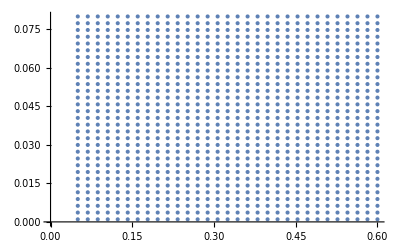

```mathematica
mtil=Table[ϕ,{ϕ,0.05,0.6,(0.6-0.05)/30}];
gtil=Table[γ,{γ,0.001,0.08,(0.08-0.001)/30}];
ϕγ=Tuples[{mtil,gtil}];
Length[ϕγ]
ListPlot[ϕγ]
```

```mathematica
results=Table[Module[{ϕ=ϕγ[[i,1]],γ=ϕγ[[i,2]],init={0,-0.05,1,0.04,0,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=-0.05,ys={},times={},zt,notfall},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];
ys=Append[ys,output[[4]]];
times=Append[times,output[[3]]];
notfall=True;
While[Or@@Thread[Abs[output[[2]]]>=10^-4]&&iteration<=200&&AllTrue[Flatten[Delete[output,4]],NumericQ]&&notfall,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
ys=Append[ys,output[[4]]];
times=Append[times,output[[3]]];

zt=Piecewise[Table[{ys[[i]],times[[i,1]]<=t<=times[[i,2]]},{i,1,Length[ys]}]];
notfall=Quiet@Check[AllTrue[Flatten[Table[zt/.t->t,{t,0,output[[1,6]],0.3}]],#>0&],False];

iteration++;];





{output,iteration,ys,times,notfall}

],{i,1,Length[ϕγ]}];
```

$Aborted

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[ϕγ]}];
```

```mathematica
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Map[Last,results];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[ϕγ,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
```

```mathematica
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
```

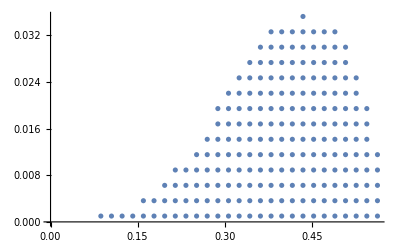

```mathematica
ListPlot[ϕγU]
```

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=ϕγU;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0866667,0.001},{0.16,0.00363333},{0.196667,0.00626667},{0.215,0.0089},{0.251667,0.0115333},{0.27,0.0141667},{0.288333,0.0194333},{0.306667,0.0220667},{0.288333,0.0168},{0.325,0.0247},{0.343333,0.0273333},{0.361667,0.0299667},{0.38,0.0326},{0.435,0.0352333},{0.49,0.0326},{0.508333,0.0299667},{0.508333,0.0273333},{0.526667,0.0247},{0.526667,0.0220667},{0.545,0.0194333},{0.545,0.0168},{0.545,0.0141667},{0.563333,0.0115333},{0.563333,0.0089},{0.563333,0.00626667},{0.563333,0.00363333},{0.563333,0.001},{0.545,0.001},{0.526667,0.001},{0.508333,0.001},{0.49,0.001},{0.471667,0.001},{0.453333,0.001},{0.435,0.001},{0.416667,0.001},{0.398333,0.001},{0.38,0.001},{0.361667,0.001},{0.343333,0.001},{0.325,0.001},{0.306667,0.001},{0.288333,0.001},{0.27,0.001},{0.251667,0.001},{0.233333,0.001},{0.215,0.001},{0.196667,0.001},{0.178333,0.001},{0.16,0.001},{0.141667,0.001},{0.123333,0.001},{0.105,0.001}}

```mathematica
boundary={{0.08666666666666667,0.001},{0.15999999999999998,0.0036333333333333335},{0.19666666666666666,0.006266666666666667},{0.21499999999999997,0.008900000000000002},{0.25166666666666665,0.011533333333333333},{0.26999999999999996,0.014166666666666668},{0.2883333333333333,0.019433333333333334},{0.3066666666666666,0.02206666666666667},{0.2883333333333333,0.016800000000000002},{0.32499999999999996,0.024700000000000003},{0.34333333333333327,0.027333333333333334},{0.3616666666666666,0.02996666666666667},{0.37999999999999995,0.032600000000000004},{0.43499999999999994,0.03523333333333334},{0.48999999999999994,0.032600000000000004},{0.5083333333333333,0.02996666666666667},{0.5083333333333333,0.027333333333333334},{0.5266666666666666,0.024700000000000003},{0.5266666666666666,0.02206666666666667},{0.5449999999999999,0.019433333333333334},{0.5449999999999999,0.016800000000000002},{0.5449999999999999,0.014166666666666668},{0.5633333333333332,0.011533333333333333},{0.5633333333333332,0.008900000000000002},{0.5633333333333332,0.006266666666666667},{0.5633333333333332,0.0036333333333333335},{0.5633333333333332,0.001},{0.5449999999999999,0.001},{0.5266666666666666,0.001},{0.5083333333333333,0.001},{0.48999999999999994,0.001},{0.47166666666666657,0.001},{0.45333333333333325,0.001},{0.43499999999999994,0.001},{0.4166666666666666,0.001},{0.39833333333333326,0.001},{0.37999999999999995,0.001},{0.3616666666666666,0.001},{0.34333333333333327,0.001},{0.32499999999999996,0.001},{0.3066666666666666,0.001},{0.2883333333333333,0.001},{0.26999999999999996,0.001},{0.25166666666666665,0.001},{0.23333333333333328,0.001},{0.21499999999999997,0.001},{0.19666666666666666,0.001},{0.1783333333333333,0.001},{0.15999999999999998,0.001},{0.14166666666666666,0.001},{0.12333333333333332,0.001},{0.105,0.001}};
```

1066

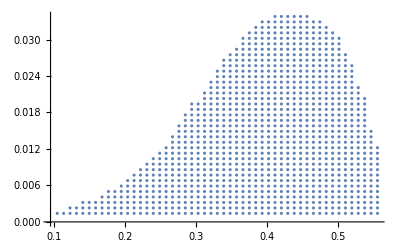

```mathematica
ϕγ=genetratepoint[boundary,0.105,0.65,0.009,0.0005,0.04,0.0009];
ϕγ[[2]]
ListPlot[ϕγ[[1]]]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\ForAntY4points.mx",ϕγ[[1]]];
```

```mathematica
results=Table[Module[{ϕ=ϕγ[[1,i,1]],γ=ϕγ[[1,i,2]],init={0,-0.05,1,0.04,0,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=-0.05,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,meanh},(*Initial state*)

output=functionSolve2[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve2[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]]];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
meanh=(zmin+zmax)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];





{output,iteration,{percentCong,amp,energyC,meanh}}

],{i,1,ϕγ[[2]]}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\ForAntY4.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code\\Feasible Region Charactersitics\\ForAntY4.mx"];
```

```mathematica
resultsUU=Quiet[Table[ReplacePart[Quiet[results[[i]]],1->Quiet[Delete[results[[i,1]],4]]],{i,1,ϕγ[[2]]}]];
```

```mathematica
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points,truefalse2,ttff,TTFF},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
truefalse2=Table[results[[i,2]]<1000,{i,1,Length[results]}];
ttff=Transpose[{truefalse,truefalse2}];
TTFF=AllTrue[#,TrueQ]&/@ttff;
trueresults=Pick[results,TTFF];
trueϕγ=Pick[ϕγ[[1]],TTFF];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
```

```mathematica
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
effic=0.5 speedND^2/engC*100;
cot=engC/steplength;
grf=grffunc[results,resultsUU];
```

```mathematica
pointsSL=MapThread[Append,{ϕγU,steplength}];
pointsV=MapThread[Append,{ϕγU,speedND}];
pointsSF=MapThread[Append,{ϕγU,stepFreq}];
pointsPC=MapThread[Append,{ϕγU,perCong}];
pointsCon=MapThread[Append,{ϕγU,convergP}];
pointsamp=MapThread[Append,{ϕγU,amp}];
pointsengC=MapThread[Append,{ϕγU,engC}];
pointsmeanh=MapThread[Append,{ϕγU,meanh}];
pointseffic=MapThread[Append,{ϕγU,effic}];
pointcot=MapThread[Append,{ϕγU,cot}];
pointgrf=MapThread[Append,{ϕγU,grf}];

frequencypercent=Abs[(1/(2Pi)-(stepFreq))2Pi]*100;
 pointpercentage=MapThread[Append,{ϕγU,Abs[(1/(2Pi)-(stepFreq))2Pi]*100}];
```

```mathematica
ticksFunc[steplength_,intD_,intU_]:=Module[{ticks,ticks1,mticks},ticks=Table[{i,Round[i,0.01]},{i,Min[steplength],Max[steplength],(Max[steplength]-Min[steplength])/(3-1)}];
ticks1=Join[{{First[ticks][[1]]+intD,Round[First[ticks][[2]],0.01],0.011}},Most[Rest[ticks]],{{Last[ticks][[1]]-intU,Round[Last[ticks][[2]],0.01]}}];
mticks=Table[{i,""},{i,Min[steplength],Max[steplength],(Max[steplength]-Min[steplength])/(13-1)}];{ticks1,mticks} ]

tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.015}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
side=0.01;
scale=(Differences[MinMax[Last/@ϕγ[[1]]]]/Differences[MinMax[First/@ϕγ[[1]]]])[[1]];
```

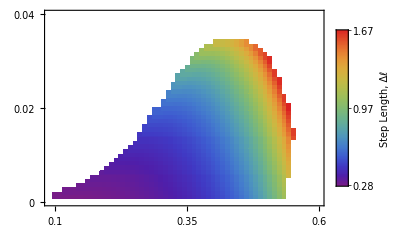

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsSL,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[steplength,0.01,0.0001];
ll2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.015],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[steplength]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],
PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[steplength]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Step
Length, Δℓ",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

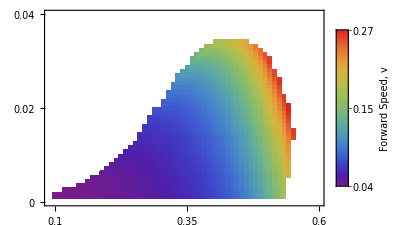

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsV,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[speedND,0.001,0.000];
s2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.015],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[speedND]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[speedND]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Roman 10"},LegendLabel->"Forward
Speed, v",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

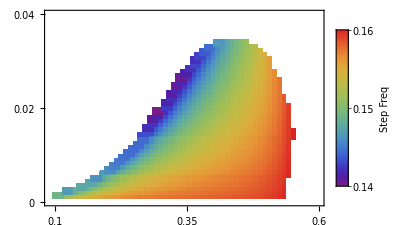

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsSF,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[stepFreq,0.000,0.000];
sF2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.014],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[stepFreq]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[stepFreq]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Step
Freq",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

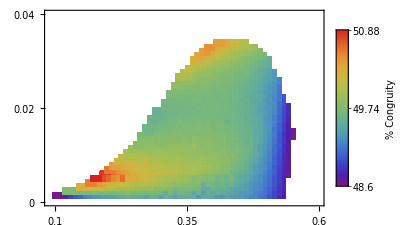

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsPC,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[perCong,0.00,0.001];
pc2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.014],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[perCong]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[perCong]},LegendMarkerSize->130,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"% Congruity",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

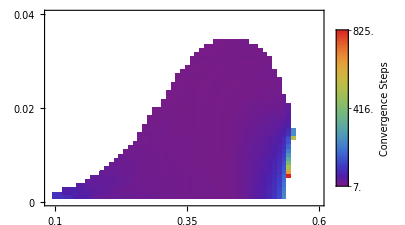

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsCon,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.001};*)
ticks=ticksFunc[convergP,0.001,0.1];
cs2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.014],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[convergP]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[convergP]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Convergence
Steps",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

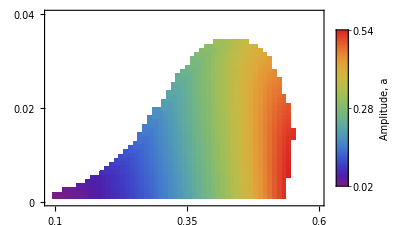

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsamp,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[amp,0.001,0.00];
amp2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[amp]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[amp]},LegendMarkerSize->150,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Amplitude, a",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

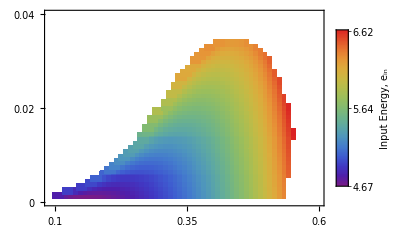

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsengC,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[engC,0.01,0.01];
ec2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[engC]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[engC]},LegendMarkerSize->110,LabelStyle->{Black,20,FontFamily->"Latin Modern Roman 10"},LegendLabel->"Input
Energy, e_in",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

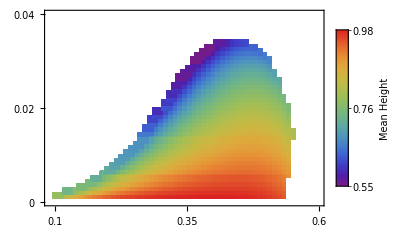

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointsmeanh,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[meanh,0.001,0.000];
mh2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[meanh]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[meanh]},LegendMarkerSize->110,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Mean
Height",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

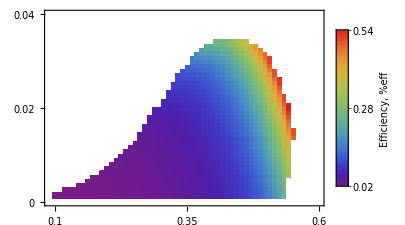

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointseffic,{-First[#]&}],#[[2]]&];
ticks=ticksFunc[effic,0.0001,0.00001];
eff2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[effic]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[effic]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Roman 10"},LegendLabel->"Efficiency,
%eff",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

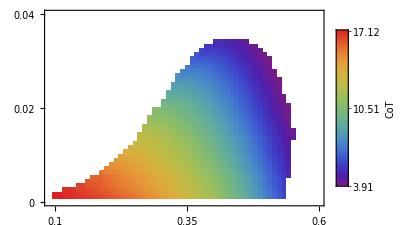

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointcot,{-First[#]&}],#[[2]]&];
ticks=ticksFunc[cot,0.001,0.1];
cot2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[cot]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[cot]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"CoT",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

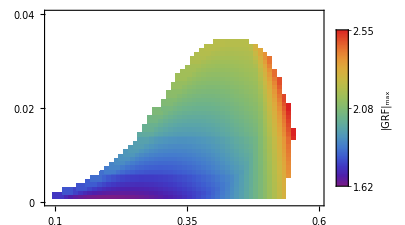

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointgrf,{-First[#]&}],#[[2]]&];
ticks=ticksFunc[grf,0.001,0.001];
grf2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.018],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[grf]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[grf]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"|GRF|_max",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

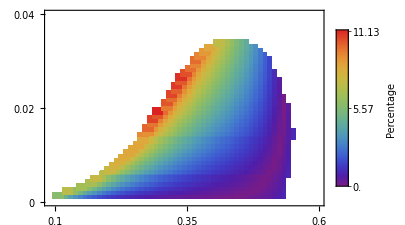

```mathematica
arrangepoints=Values@GroupBy[SortBy[pointpercentage,{-First[#]&}],#[[2]]&];
(*offsetdata=ldev2P[[3]]/.{x_,y_}:>{x,y+0.01};*)
ticks=ticksFunc[frequencypercent,0.01,0.1];
pp2=Legended[Show[Graphics[Table[Table[{Directive[Thickness[0.015],ColorData["Rainbow"][Rescale[arrangepoints[[j,i,3]],MinMax[frequencypercent]]]],Rectangle[arrangepoints[[j,i]][[;;2]]-{side,side*scale},arrangepoints[[j,i]][[;;2]]+{side,side*scale}]},{i,1,Length[arrangepoints[[j]]]}],{j,1,Length[arrangepoints]}],Frame->True,LabelStyle->{Black,22,FontFamily->"Latin Modern Math"}(*,FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}}*),AspectRatio->2/3,Axes->False,ImageSize->{340,230}],
PlotRange->{{0.09,0.6},{0,0.04}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.35,0.6}],Automatic}}

],

BarLegend[{"Rainbow",MinMax[frequencypercent]},LegendMarkerSize->120,LabelStyle->{Black,20,FontFamily->"Latin Modern Math"},LegendLabel->"Percentage",Ticks->Join[ticks[[1]],ticks[[2]]]]
]
```

```mathematica
plot=Show[GraphicsGrid[{{ll2,s2,ec2,mh2},{amp2,pc2,eff2,cot2}},ImageSize->{1600,490},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["a",22,FontFamily->"Latin Modern Math"],{20,5}],
Text[Style["b",22,FontFamily->"Latin Modern Math"],{410,5}],
Text[Style["c",22,FontFamily->"Latin Modern Math"],{800,5}],
Text[Style["d",22,FontFamily->"Latin Modern Math"],{1175,5}],
Text[Style["e",22,FontFamily->"Latin Modern Math"],{20,-190}],
Text[Style["f",22,FontFamily->"Latin Modern Math"],{410,-190}],
Text[Style["g",22,FontFamily->"Latin Modern Math"],{800,-190}],
Text[Style["h",22,FontFamily->"Latin Modern Math"],{1175,-190}],
Text[Style[Rotate["Inverse Froude Number",Pi/2],26,FontFamily->"Latin Modern Math"],{-10,-180}],
Text[Style["Frequency Ratio",26,FontFamily->"Latin Modern Math"],{740,-415}]

}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\GaitChar.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\GaitChar.pdf

```mathematica
plotA=Show[GraphicsGrid[{{ec2,eff2},{cot2,pc2}},ImageSize->{1000,530},Spacings->{Scaled[0],Scaled[0.1]}],
Graphics[{Text[Style["a",22,FontFamily->"Latin Modern Math"],{35,10}],
Text[Style["b",22,FontFamily->"Latin Modern Math"],{485,10}],
Text[Style["c",22,FontFamily->"Latin Modern Math"],{35,-245}],
Text[Style["d",22,FontFamily->"Latin Modern Math"],{485,-245}],

Text[Style[Rotate["Inverse Froude Number, γ",Pi/2],20,FontFamily->"Latin Modern Roman 10"],{-15,-220}],
Text[Style["Frequency Ratio, φ",20,FontFamily->"Latin Modern Roman 10"],{410,-490}]

}]

]
```

-Graphics-

```mathematica
plotB=Show[GraphicsGrid[{{ll2,s2,mh2},{amp2,cs2,grf2}},ImageSize->{1500,600},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["a",22,FontFamily->"Latin Modern Math"],{40,5}],
Text[Style["b",22,FontFamily->"Latin Modern Math"],{500,5}],
Text[Style["c",22,FontFamily->"Latin Modern Math"],{950,5}],
Text[Style["d",22,FontFamily->"Latin Modern Math"],{35,-230}],
Text[Style["e",22,FontFamily->"Latin Modern Math"],{490,-230}],
Text[Style["f",22,FontFamily->"Latin Modern Math"],{950,-230}],

Text[Style[Rotate["Inverse Froude Number, γ",Pi/2],20,FontFamily->"Latin Modern Math"],{-0,-200}],
Text[Style["Frequency Ratio, φ",20,FontFamily->"Latin Modern Math"],{630,-460}]

}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\GaitCharA.pdf",plotA]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\GaitCharA.pdf

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\GaitCharB.pdf",plotB]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\GaitCharB.pdf